# Test suite of pd codes.

--Jason, May 2014. 

This notebook uses KnotTheory to come up with a list of pd codes and HOMFLY polynomials, then converts them into a format that plcurve can read. This autogenerates data used by test_homfly.

```mathematica
AppendTo[$Path,NotebookDirectory[]]
```

{/Applications/Mathematica.app/SystemFiles/Links,/Users/cantarel/Library/Mathematica/Kernel,/Users/cantarel/Library/Mathematica/Autoload,/Users/cantarel/Library/Mathematica/Applications,/Library/Mathematica/Kernel,/Library/Mathematica/Autoload,/Library/Mathematica/Applications,.,/Users/cantarel,/Applications/Mathematica.app/AddOns/Packages,/Applications/Mathematica.app/AddOns/LegacyPackages,/Applications/Mathematica.app/SystemFiles/Autoload,/Applications/Mathematica.app/AddOns/Autoload,/Applications/Mathematica.app/AddOns/Applications,/Applications/Mathematica.app/AddOns/ExtraPackages,/Applications/Mathematica.app/SystemFiles/Kernel/Packages,/Applications/Mathematica.app/Documentation/English/System,/Applications/Mathematica.app/SystemFiles/Data/ICC,/Users/cantarel/plcurve/data/KnotTheory/,/Users/cantarel/plcurve/data/KnotTheory,/Users/cantarel/plcurve/data/}

```mathematica
<<KnotTheory`
```

Loading KnotTheory` version of April 3, 2014, 16:23:56.0784.
Read more at http://katlas.org/wiki/KnotTheory.

The basic idea is that we can load the existing pd codes with the “AllKnots” command:

```mathematica
AllKnots[5]
```

{Knot[5,1],Knot[5,2]}

and convert them into KnotTheory’s version of PD codes with PD:

```mathematica
ListofPDs = PD /@ AllKnots[{3,11}];
```

```mathematica
Export[NotebookDirectory[] <> "../test/rolfsentable.txt",Prepend[ListofPDs,"pdcodes " <> ToString[Length[ListofPDs]]]]
```

/Users/cantarel/plcurve/data/../test/rolfsentable.txt

```mathematica
ListofLinkPDs = PD /@ AllLinks[{3,11}];
```

KnotTheory::loading: Loading precomputed data in "PD4Links`".

```mathematica
Export[NotebookDirectory[] <> "../test/thistlethwaitetable.txt",Prepend[ListofLinkPDs,"pdcodes " <> ToString[Length[ListofLinkPDs]]]]
```

/Users/cantarel/plcurve/data/../test/thistlethwaitetable.txt

We now output the HOMFLY polynomial for each of these. In order to read these in for testing, we’ll need to break the nice mathematica output so that, for instance, no coefficient explicitly writes a “1” and a^0 and z^0 are not auto-simplified to 1.

```mathematica
FixMon[m_] := If[Exponent[m,a] == 0 && Exponent[m,z] == 0, {m,0,0},{m/(a^Exponent[m,a] z^Exponent[m,z]),Exponent[m,a],Exponent[m,z]}];

Stringize[{k_,l1_,l2_}] := ToString[k] <> " a^" <> ToString[l1] <> " z^" <> ToString[l2];

CHOMFLYPT[MyPD_] := 
StringJoin[Riffle[Stringize /@ (FixMon /@ (List@@HOMFLYPT[MyPD][I a,I z]))," + "]];
```

```mathematica
ListofHOMFLYPTS = CHOMFLYPT /@ ListofPDs;
```

```mathematica
Export[NotebookDirectory[] <> "rolfsenhomflys.txt",Prepend[ListofHOMFLYPTS,"homfly polynomials " <> ToString[Length[ListofHOMFLYPTS]]]]
```

/Users/cantarel/plcurve/data/rolfsenhomflys.txt

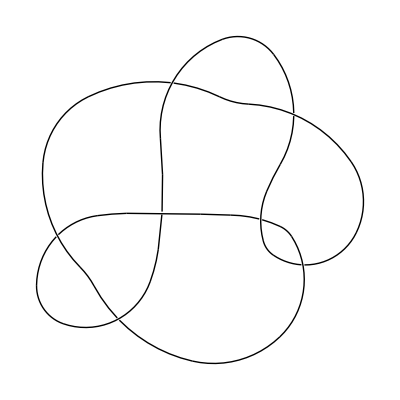

```mathematica
DrawPD[ListofPDs[[13]]]
```

```mathematica
HOMFLYPT[ListofPDs[[1]]][ a,-z]
```

2 a^2-a^4+a^2 z^2

Ok, so a puzzle: our ccode converter gives us

1+3b2a2d3c
2+1b3a3d1c
3+2b1a1d2c

for the PD code

```mathematica
PD[Knot[3,1]]
```

PD[X[1,4,2,5],X[3,6,4,1],X[5,2,6,3]]

And lmpoly gives us the

```mathematica
HOMFLYPT[Knot[3,1]][I a,I z]
```

-2 a^2-a^4+a^2 z^2

KnotTheory::credits: "DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004."

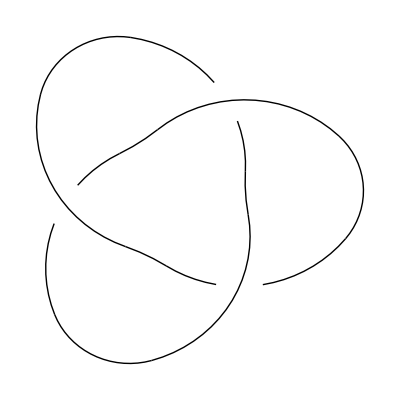

```mathematica
DrawPD[Knot[3,1]]
```